# GLOG

The generalized log transformation (glog),

glog(x)=log (x+√(x^2+a^2))/2

is used.  The glog transformation can be derived as the appropriate variance stablizing transformation in this case.  Also the glog transformation is more reasonable for small values than the log or shifited log, that is, log(x+a).  The glog transformation was introduced in microarrays.  In the plot below a=1.

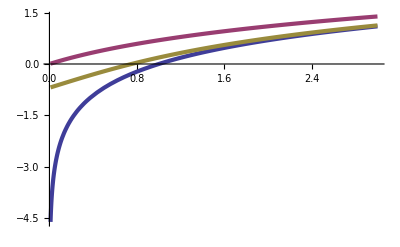

#### Inverse Function

```mathematica
Solve[G==Log[(x+Sqrt[x^2+a^2])/2],x]
```

{{x→1/4 ⅇ^-G (-a^2+4 ⅇ^(2 G))}}

0.25*exp(-x)*(4*exp(2*x)-(a*a))

### Reference

W. Huber, A. von Heydebreck, H. Sultmann, A. Poustka, and M. Vingron. Variance stablization applied to microarray data calibration and to quantification of differential expression. Bioinformatics, 18:S96{S104, 2002.

#### Code

```mathematica
Needs["PlotLegends`"];
L=Style[#,14]&/@{"log","slog","glog"};Plot[{Log[x],Log[x+1],Log[(x+Sqrt[x^2+1])/2]},{x,0.01,3},
PlotStyle->{AbsoluteThickness[3]},PlotRange->All,PlotLegend->L,LegendPosition->{0.1,-0.5},
LegendSize->{0.5,0.5}]
```

-Graphics-